```mathematica
M = {{σ+1, 3},{-2, σ-1}}
x=.;y=.
X[t_]={x[t],y[t]};
system = X'[t] == M.X[t]
```

{{1+σ,3},{-2,-1+σ}}

{x'[t],y'[t]}=={(1+σ) x[t]+3 y[t],-2 x[t]+(-1+σ) y[t]}

```mathematica
sol=DSolve[system,{x,y},t]
```

{{x→Function[{t},(3 ⅇ^(t σ) C[2] Sin[√5 t])/(√5)+1/5 ⅇ^(t σ) C[1] (5 Cos[√5 t]+√5 Sin[√5 t])],y→Function[{t},-(2 ⅇ^(t σ) C[1] Sin[√5 t])/(√5)+1/5 ⅇ^(t σ) C[2] (5 Cos[√5 t]-√5 Sin[√5 t])]}}

```mathematica
X[t_,x0_,y0_,σ_]={x[t],y[t]}/.sol/.{C[1]->x0, C[2]->y0}
```

{{(3 ⅇ^(t σ) y0 Sin[√5 t])/(√5)+1/5 ⅇ^(t σ) x0 (5 Cos[√5 t]+√5 Sin[√5 t]),-(2 ⅇ^(t σ) x0 Sin[√5 t])/(√5)+1/5 ⅇ^(t σ) y0 (5 Cos[√5 t]-√5 Sin[√5 t])}}

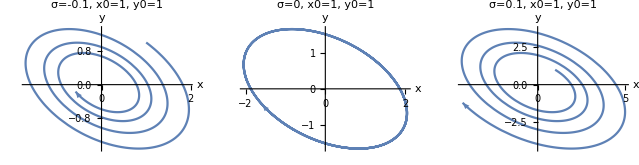

/Users/adam/Programming/CAS/Dynamical Systems/Assignment 1/two-dim-lin-sys.png

```mathematica
p1=ParametricPlot[X[t,1,1,-0.1],{t,0,10}, AxesLabel->{"x","y"}, PlotLabel->"σ=-0.1, x0=1, y0=1"]/.Line->Arrow;
p2=ParametricPlot[X[t,1,1,0],{t,0,10},AxesLabel->{"x","y"}, PlotLabel->"σ=0, x0=1, y0=1"]/.Line->Arrow;
p3=ParametricPlot[X[t,1,1,0.1],{t,0,10},AxesLabel->{"x","y"}, PlotLabel->"σ=0.1, x0=1, y0=1"]/.Line->Arrow;
g= GraphicsRow[{p1,p2,p3}]
Export["/Users/adam/Programming/CAS/Dynamical Systems/Assignment 1/two-dim-lin-sys.png",g,"PNG", ImageSize->{1500}]
```

```mathematica
Solve [X[0,x0,y0,0]== X[t,x0,y0,0],t]
```

{{t→ConditionalExpression[(2 π C[1])/(√5),C[1]∈ℤ]}}

```mathematica
Xsimp[t_,x0_,y0_] = X[t,x0,y0,0] //Simplify
```

{{x0 Cos[√5 t]+((x0+3 y0) Sin[√5 t])/(√5),y0 Cos[√5 t]-((2 x0+y0) Sin[√5 t])/(√5)}}

```mathematica
R[t_] =Xsimp[t,x0,y0][[1]][[1]]^2  + Xsimp[t,x0,y0][[1]][[2]]^2 //Simplify
```

(y0 Cos[√5 t]-((2 x0+y0) Sin[√5 t])/(√5))^2+(x0 Cos[√5 t]+((x0+3 y0) Sin[√5 t])/(√5))^2

```mathematica
dR[t_] = D[R[t],t]//Simplify
T = Simplify[Solve[dR[t]==0,t]]
```

2 (x0^2+x0 y0-y0^2) Cos[2 √5 t]+√5 y0 (2 x0+y0) Sin[2 √5 t]

{{t→ConditionalExpression[(ArcTan[-(√5 y0 (2 x0+y0))/(√((2 x0^2+2 x0 y0+3 y0^2)^2)),(2 (x0^2+x0 y0-y0^2))/(√((2 x0^2+2 x0 y0+3 y0^2)^2))]+2 π C[1])/(2 √5),C[1]∈ℤ]},{t→ConditionalExpression[(ArcTan[(√5 y0 (2 x0+y0))/(√((2 x0^2+2 x0 y0+3 y0^2)^2)),-(2 (x0^2+x0 y0-y0^2))/(√((2 x0^2+2 x0 y0+3 y0^2)^2))]+2 π C[1])/(2 √5),C[1]∈ℤ]}}

```mathematica
t0=ArcTan[-(√5 y0 (2 x0+y0))/(√((2 x0^2+2 x0 y0+3 y0^2)^2)),(2 (x0^2+x0 y0-y0^2))/(√((2 x0^2+2 x0 y0+3 y0^2)^2))]/(2 √5)
t1=ArcTan[(√5 y0 (2 x0+y0))/(√((2 x0^2+2 x0 y0+3 y0^2)^2)),-(2 (x0^2+x0 y0-y0^2))/(√((2 x0^2+2 x0 y0+3 y0^2)^2))]/(2 √5)
```

ArcTan[-(√5 y0 (2 x0+y0))/(√((2 x0^2+2 x0 y0+3 y0^2)^2)),(2 (x0^2+x0 y0-y0^2))/(√((2 x0^2+2 x0 y0+3 y0^2)^2))]/(2 √5)

ArcTan[(√5 y0 (2 x0+y0))/(√((2 x0^2+2 x0 y0+3 y0^2)^2)),-(2 (x0^2+x0 y0-y0^2))/(√((2 x0^2+2 x0 y0+3 y0^2)^2))]/(2 √5)

```mathematica
Simplify[R[t0]/R[t1], {x0∈Reals, y0∈Reals}]
```

1/2 (3+√5)

```mathematica
x0=.; y0=.
dir = Xsimp[t0,x0,y0] //Simplify
x0=1;y0=1;
dir
ans = Normalize[dir[[1]]] //Simplify//TrigReduce//Expand//TrigExpand//PowerExpand//Simplify
N[ans]
```

{{x0 Cos[1/2 ArcTan[-(√5 y0 (2 x0+y0))/(√((2 x0^2+2 x0 y0+3 y0^2)^2)),(2 (x0^2+x0 y0-y0^2))/(√((2 x0^2+2 x0 y0+3 y0^2)^2))]]+((x0+3 y0) Sin[1/2 ArcTan[-(√5 y0 (2 x0+y0))/(√((2 x0^2+2 x0 y0+3 y0^2)^2)),(2 (x0^2+x0 y0-y0^2))/(√((2 x0^2+2 x0 y0+3 y0^2)^2))]])/(√5),y0 Cos[1/2 ArcTan[-(√5 y0 (2 x0+y0))/(√((2 x0^2+2 x0 y0+3 y0^2)^2)),(2 (x0^2+x0 y0-y0^2))/(√((2 x0^2+2 x0 y0+3 y0^2)^2))]]-((2 x0+y0) Sin[1/2 ArcTan[-(√5 y0 (2 x0+y0))/(√((2 x0^2+2 x0 y0+3 y0^2)^2)),(2 (x0^2+x0 y0-y0^2))/(√((2 x0^2+2 x0 y0+3 y0^2)^2))]])/(√5)}}

{{Cos[1/2 (π-ArcTan[2/(3 √5)])]+(4 Sin[1/2 (π-ArcTan[2/(3 √5)])])/(√5),Cos[1/2 (π-ArcTan[2/(3 √5)])]-(3 Sin[1/2 (π-ArcTan[2/(3 √5)])])/(√5)}}

{-1/10 (-5+√5) √(5+2 √5),-(3+√5)/(√(50+22 √5))}

{0.850651,-0.525731}

```mathematica
2abc/.abc->3
```

6